## Free Fermions

```mathematica
<<MaTeX`
```

```mathematica
(* if you don't have MaTeX installed yet, do it, it's a cool LaTeX compiler for Mathematica :)
download the paclet at https://github.com/szhorvat/MaTeX to your ~/Downoads folder and execute this cell *)
(*Needs["PacletManager`"]
PacletInstall["~/Downloads/MaTeX-1.7.6.paclet"]*)
```

```mathematica
L=128; (* number of Sites *)
t=1; (* intra-wire hopping *)
omega=.05; (* inter-wire hopping *)
NN=52;(* number of particles *)

GGs={}; (* single-particle Green's function *)
chis={}; (* plaquette fluxes *)
Do[
HH =ConstantArray[0,{2L,2L}];
Do[
HH[[2*i-1,2*(i+1)-1]]=-t*ⅇ^(ⅈ*chi/2);
HH[[2*i,2*(i+1)]]=-t*ⅇ^(-ⅈ*chi/2);
,{i,1,L-1}];
Do[
HH[[2*i-1,2*i]]=omega;
,{i,1,L}];
HH=HH+HH†;
{evals,evecs}=Eigensystem[HH];
order=Ordering[evals];
DD=DiagonalMatrix[evals[[order]]];
UU=evecs[[order]]*;
GG=UUᵀ[[;;,1;;NN]].UU[[1;;NN,;;]]*;
AppendTo[GGs,GG];
AppendTo[chis,chi];
If[Length[DeleteDuplicates[Flatten[Chop[UU†.DD.UU-HH,10^-12]]]]≠1,Print["Something went wrong."]];
,{chi,0.,2π,2π/(L)}]
```

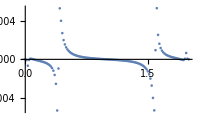

```mathematica
ListPlot[Table[{chis[[i]]/π,2Im[Mean[Diagonal[GGs[[i]],2][[;;;;2]]*ⅇ^(ⅈ*chis[[i]]/2)]]},{i,1,Length[chis]}],PlotRange->Full,AxesLabel->MaTeX[{"\\chi/\\pi","j_c/t"}]]
```

0.0625

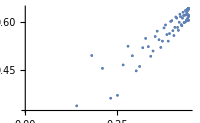

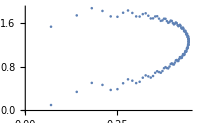

```mathematica
jj=5;
GG=GGs[[jj]];
chis[[jj]]/π

nnexp[x_,α_,y_,β_]:=GG[[2*x-1+α,2*x-1+α]]*GG[[2*y-1+β,2*y-1+β]] + GG[[2*x-1+α,2*y-1+β]]*(KroneckerDelta[x,y]*KroneckerDelta[α,β]-GG[[2*y-1+β,2*x-1+α]])

ListPlot[Nfluct=Table[{1/π^2 Log[2L/π*Sin[π*ell/L]],
Sum[nnexp[x,0,y,0]+nnexp[x,1,y,1]+nnexp[x,0,y,1]+nnexp[x,1,y,0],{x,1,ell},{y,1,ell}]-Sum[nnexp[x,0,x,0]+nnexp[x,1,x,1],{x,1,ell}]^2},{ell,1,L-1}],AxesLabel->MaTeX[{"\\ell","\\langle(N_\\ell - \\langle N_\\ell\\rangle)^2\\rangle"}]]

ListPlot[Zfluct=Table[{1/π^2 Log[2L/π*Sin[π*ell/L]],Sum[nnexp[x,0,y,0]+nnexp[x,1,y,1]-nnexp[x,0,y,1]-nnexp[x,1,y,0],{x,1,ell},{y,1,ell}]-Sum[nnexp[x,0,x,0]-nnexp[x,1,x,1],{x,1,ell}]^2},{ell,1,L-1}],AxesLabel->MaTeX[{"\\ell","\\langle(Z_\\ell - \\langle Z_\\ell\\rangle)^2\\rangle"}]]
```

```mathematica
NonlinearModelFit[Nfluct,a*x+b,{a,b},x]
NonlinearModelFit[Zfluct,a*x+b,{a,b},x]
```

FittedModel[0.169779+1.02766 x]

FittedModel[0.901735+0.826288 x]